```mathematica
Clear["Global`*"];
SetDirectory@NotebookDirectory[];
```

# User Guide: How to Fix the House of Representatives

Okay, we have everything we need to start a computational experiment on how the House of Representatives--and, by extension, the Electoral College--could be adjusted for better representation without the need for a Constitutional amendment. In the process of toying with the size of the House and the algorithm for how the seats are allotted, we’ll be recalculating the results of the 2016 election if our adjustments were to have taken place.

## Loading the data and the functions

I’ve collected data on historical apportionment, populations, and 2016 election results. All the notebooks are in the README. The data is loaded by two packages, `elections.m` and `apportionment.m`, which is loaded by `election.m`.

Results of the 2016 presidential and House of Representatives elections are also backed into the elections package.

```mathematica
CloudGet["https://www.wolframcloud.com/objects/8549bab6-7b14-4b2a-b77a-8944882d6562"]
```

## The Variables

The Constitution stipulates that the number of representatives per state should be reapportioned after each decennial census based on state populations. It does not specify the total number of representatives or the exact method of allotment, other than specifying that each state should have at least one representative.

Since the 1940 Census, the United States has used the Huntington-Hill algorithm, known as the "method of equal proportions," to divvy up the 435 House seats. This begins by allotting one electoral vote to each state, leaving 385 left. The 50 states are then allotted these remaining seats one-by-one according to which one has the highest priority as determined by a simple equation: its population divided by the square root of its current seats times one extra seat (the Geometric Mean):

P/(√(n (1+n)))

We’re going to start by using this algorithm and adjusting the size and default starting and ending points. Then we’ll toy around with other algorithms. Each one we consider will take just two arguments: The population of the state and its current number of seats during the iterative process of assigning them, like so:

PriorityHuntingtonHill[stateAbbr_, stateEVs_] := 
	1.0 * statesByAbbreviation[stateAbbr][“population_decennial”][“2010”] / 	Sqrt[stateEVs * (stateEVs + 1)]

To run a new apportionment, you just specify the total number of seats, how many each state begins with, how many to add or subtract at the end of the allocation, and the algorithm, which defaults to `PriorityHuntingtonHill`:

total_ is the total number of seats to allocate, defaulting to 435

min_ is the default number of seats that every state begins with, defaulting to 1

bonus_ is the number of seats every state gets at the end of the process, after total_ is depleted. Default is 0. Setting to 2 calculates electoral votes by accounting for senators, so long as you remember to add 3 for Washington, D.C.!

priorityFunc_ is the means of determining a state's priority, defaulting to the Huntington-Hill function defined above

For example, here’s how a much larger, 1,000-person House would look if we started everyone with 0 seats, were assigned 950, and then given a bonus of 1 at the end just to make sure no one goes without.

```mathematica
bigHouse = CalculateAllocations[1000, 0, 1]
```

<|AK→3,AL→16,AR→10,AZ→21,CA→116,CO→16,CT→12,DE→4,FL→59,GA→31,HI→5,IA→10,ID→6,IL→40,IN→21,KS→10,KY→14,LA→15,MA→21,MD→19,ME→5,MI→31,MN→17,MO→19,MS→10,MT→4,NC→30,ND→3,NE→7,NH→5,NJ→28,NM→7,NV→9,NY→61,OH→37,OK→13,OR→13,PA→40,RI→4,SC→15,SD→4,TN→21,TX→78,UT→10,VA→26,VT→3,WA→22,WI→19,WV→7,WY→3|>

## Visualizing Your Allocation

There are a few ways to see how your allocation departs from the current one. You can make a grid (the second argument is number of states per row):

```mathematica
HorizontalGrid[bigHouse, 26]
```

state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
actual | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2 | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
yours | 3 | 16 | 10 | 21 | 116 | 16 | 12 | 4 | 59 | 31 | 5 | 10 | 6 | 40 | 21 | 10 | 14 | 15 | 21 | 19 | 5 | 31 | 17 | 19 | 10 | 4
delta | 2 | 9 | 6 | 12 | 63 | 9 | 7 | 3 | 32 | 17 | 3 | 6 | 4 | 22 | 12 | 6 | 8 | 9 | 12 | 11 | 3 | 17 | 9 | 11 | 6 | 3
state | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2 | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
yours | 30 | 3 | 7 | 5 | 28 | 7 | 9 | 61 | 37 | 13 | 13 | 40 | 4 | 15 | 4 | 21 | 78 | 10 | 26 | 3 | 22 | 19 | 7 | 3 | 1000
delta | 17 | 2 | 4 | 3 | 16 | 4 | 5 | 34 | 21 | 8 | 8 | 22 | 2 | 8 | 3 | 12 | 42 | 6 | 15 | 2 | 12 | 11 | 4 | 2 | 565

You can map the difference as well.

```mathematica
MapDiffs[bigHouse]
```

-Graphics-
-Graphics--Graphics-

## But is Our New Allocation Fair?

In an ideal world, every state would have the same ratio of representatives-to-people. We can at least chart see how different some states are from others. I find the coefficient of variation is a useful measure since the standard deviation depends on the number of members.

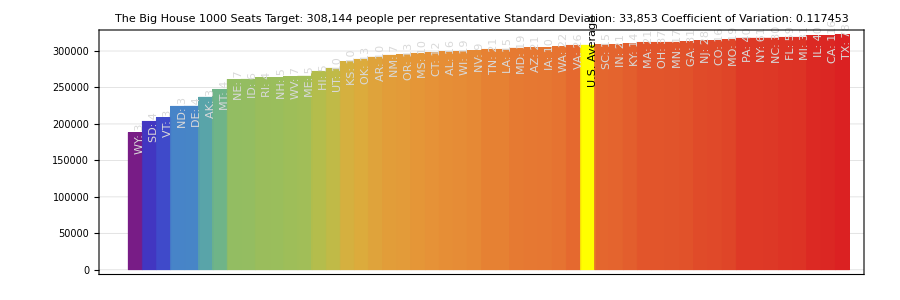

```mathematica
VisualizeRepresentation[bigHouse, "The Big House"]
```

By comparison, the current allocation does a little better. I’ve already loaded an accurate variable called `houseOfRepresentatives`

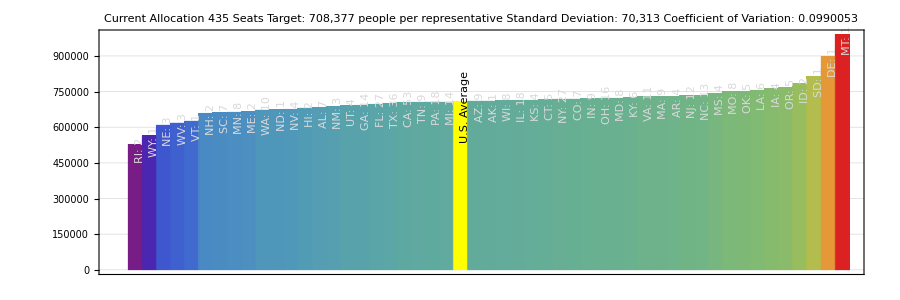

```mathematica
VisualizeRepresentation[houseOfRepresentatives, "Current Allocation"]
```

Okay, great. Now let’s see how allocations affect elections!

## Recalculating Elections

Every time we change and allotment we’ll recompute both the 2016 presidential election and estimate the partisan breakdown in the House. This isn’t too difficult for the presidency, other than estimating what might happen in Maine and Nebraska, which can divide their electors by congressional district. That happens in the `RerunElectionPresident` and `RerunElectionPresidentState` functions in the elections package:

For the House it’s more complicated. The package also has the 2016 congressional election results baked in--both the individual winners of all 435 seats by party and the statewide vote for Democratic or Republican candidates, like so:

```mathematica
electionDataCongress["CA"]
```

<|abbr→CA,entity→California, United States,votesD→8.62443×10^6,votesR→4.68203×10^6,votesTotal→1.33065×10^7,percentVoteD→0.648138,percentVoteR→0.351862,D→39,R→14,repCount→53,percentRepsD→0.735849,percentRepsR→0.264151|>

As we know, many states have horrifically gerrymandering districts to misrepresent the overall preference of the voters. However, if the size of the House were to increase dramatically--say, to 1,000 members--it would presumably be much more difficult to cook the game. So we need to gradually move from representing the partisan split by district to the vote by state as theoretical new seats emerge.

The way this will work is that, for each 25% of seats beyond the actual value, the odds with get 25% percent closer to the statewide figure. This is admittedly a bit crude, but it will serve our purposes for now. You can run any state with any number of electoral votes with `RerunElectionCongressState` or run a whole new allocation scheme with `RerunElectionCongress`

```mathematica
RerunElectionCongressState["CA", 250]
```

<|abbr→CA,D→168,R→82,total→250|>

## Running Our Allocations Through Elections

Let’s see whether our “Big House” would have altered the outcome of the 2016 elections, both for President and the House. The presidential function optionally allows you to allot more than three electoral votes to DC.

```mathematica
rerunPresidentBigHouse = RerunElectionPresident[bigHouse, 5];
rerunPresidentBigHouse["result"]
```

<|R→628,D→477,Total→1105|>

Like with allotments, we can visualize the difference:

```mathematica
MapElection[rerunPresidentBigHouse]
```

Donald Trump
-Graphics-
628Hillary Clinton
-Graphics-
477
-Graphics-
-Graphics--Graphics-

Or you can chart it:

```mathematica
ChartPresidentialElection[rerunPresidentBigHouse]
```

State | AK | AL | AR | AZ | CA | CO | CT | DC | DE | FL | GA | HI | IA | ID | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
Clinton | 0 | 0 | 0 | 0 | 118 | 18 | 14 | 5 | 6 | 0 | 0 | 7 | 0 | 0 | 42 | 0 | 0 | 0 | 0 | 23 | 21 | 6 | 0 | 19 | 0 | 0 | 0
Trump | 5 | 18 | 12 | 23 | 0 | 0 | 0 | 0 | 0 | 61 | 33 | 0 | 12 | 8 | 0 | 23 | 12 | 16 | 17 | 0 | 0 | 1 | 33 | 0 | 21 | 12 | 6
Total | 5 | 18 | 12 | 23 | 118 | 18 | 14 | 5 | 6 | 61 | 33 | 7 | 12 | 8 | 42 | 23 | 12 | 16 | 17 | 23 | 21 | 7 | 33 | 19 | 21 | 12 | 6
State | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
Clinton | 0 | 0 | 0 | 7 | 30 | 9 | 11 | 63 | 0 | 0 | 15 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 28 | 5 | 24 | 0 | 0 | 0 | 477
Trump | 32 | 5 | 9 | 0 | 0 | 0 | 0 | 0 | 39 | 15 | 0 | 42 | 0 | 17 | 6 | 23 | 80 | 12 | 0 | 0 | 0 | 21 | 9 | 5 | 628
Total | 32 | 5 | 9 | 7 | 30 | 9 | 11 | 63 | 39 | 15 | 15 | 42 | 6 | 17 | 6 | 23 | 80 | 12 | 28 | 5 | 24 | 21 | 9 | 5 | 1105

As for Congress, you can easily compare the estimated outcome of your allocation in the House:

```mathematica
rerunCongressBigHouse = RerunElectionCongress[bigHouse];
rerunCongressBigHouse["result"]
```

<|R→532,D→468,Total→1000|>

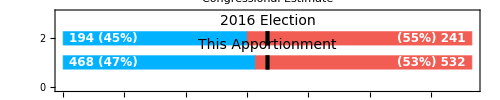

```mathematica
ChartElectionCongress[rerunCongressBigHouse]
```